```mathematica
r = 75;
```

```mathematica
space = 15;
```

```mathematica
range = 1000;
```

```mathematica
extraFineRange = 100;
```

```mathematica
extraExtraFineRange = 10;
```

```mathematica
fractionScale =( NumeratorDenominator/@Cases[Sort[Union[Flatten[Table[n/d , {n , 1 , 10} , {d , 1 ,10}]]]] , x_/;x>=1]);
```

```mathematica
fractionScale =Partition[ Riffle[fractionScale , Table[0 , {Length[fractionScale]}]] , 2]
```

{{{1,1},0},{{10,9},0},{{9,8},0},{{8,7},0},{{7,6},0},{{6,5},0},{{5,4},0},{{9,7},0},{{4,3},0},{{7,5},0},{{10,7},0},{{3,2},0},{{8,5},0},{{5,3},0},{{7,4},0},{{9,5},0},{{2,1},0},{{9,4},0},{{7,3},0},{{5,2},0},{{8,3},0},{{3,1},0},{{10,3},0},{{7,2},0},{{4,1},0},{{9,2},0},{{5,1},0},{{6,1},0},{{7,1},0},{{8,1},0},{{9,1},0},{{10,1},0}}

```mathematica
(*fractionSizeL = (((2π Log[range,(#[[1]] / #[[2]])]&/@fractionScale)-(2 π Log[range,(#[[1]] / #[[2]])]&/@RotateRight[fractionScale])))//N;*)
```

```mathematica
(*fractionSizeR = (((2π Log[range,(#[[1]] / #[[2]])]&/@RotateLeft[fractionScale])-(2π Log[range,(#[[1]] / #[[2]])]&/@fractionScale)))//N;*)
```

```mathematica
(*fractionSize = Max/@Partition[Riffle[fractionSizeL , fractionSizeR] , 2];*)
```

```mathematica
(*fractionSize = fractionSize / Max[fractionSize];*)
```

```mathematica
(*fractionFull = Partition[Riffle[fractionScale , fractionSize] , 2];*)
```

```mathematica
value[x_/;NumberQ[x]]:=x;
```

```mathematica
value[{{n_Integer , d_Integer} , s_}]:=n/d;
```

```mathematica
Options[repr]= {invert -> False};
```

```mathematica
invert::usage = "Use negative scale values.";
```

```mathematica
repr[x_/;NumberQ[x] , OptionsPattern[]]:=If[x == 1 , "" , x];
```

```mathematica
repr[{{n_Integer , d_Integer} , s_} , OptionsPattern[]]:=If[OptionValue[invert],
If[n==1,If[d == 1,"",ToString[d]],ToString[d]<>"/"<>ToString[n]],
If[d==1,If[n == 1,"",ToString[n]],ToString[n]<>"/"<>ToString[d]]];
```

```mathematica
font[x_/;NumberQ[x]]:=0;
```

```mathematica
font[{{n_Integer , d_Integer} , s_}]:=s;
```

```mathematica
regularScale = Table[i , {i , 0 ,range , 100}][[2;;]];
```

```mathematica
regularFineScale = Table[i , {i , extraFineRange ,range , 10}][[2;;]];
```

```mathematica
regularFineScaleNamed = Table[i , {i , 0 ,extraFineRange-1 , 10}][[2;;]];
```

```mathematica
regularExtraFineScale = Table[i , {i , extraExtraFineRange ,extraFineRange , 1}][[2;;]];
```

```mathematica
regularExtraFineScaleNamed = Table[i , {i , 0 ,extraExtraFineRange - 1 , 1}][[2;;]];
```

```mathematica
regularExtraExtraFineScale = Table[i , {i , 0 ,extraExtraFineRange , 0.1}][[2;;]];
```

```mathematica
shuffle::usage = "Shuffle font distances.";
```

```mathematica
Options[drawTick]:={invert ->False , shuffle->False};
```

```mathematica
drawTick[r1_ , r2_ , fontDistance_ , fontSize_ , rotText_ , OptionsPattern[]][v_]:= 
Module[{s , e , f , sg , addi},
If[OptionValue[invert] , sg = -1.0 , sg = 1.0];
(*s = N[r1{Cos[sg 2π Log[range , value[v]]] , Sin[sg 2 π Log[range , value[v]]]}];
e = N[r2{Cos[sg 2π Log[range , value[v]]] , Sin[sg 2 π Log[range , value[v]]]}];*)
addi = Sign[r2 - r1] font[v];
(*addi = If[font[v] * r2 < 10 , r2 + fontDistance - 5 , r2 + fontDistance];*)
If[Not[OptionValue[shuffle]],
addi = 0;
];
s = N[r1{Cos[sg 2π Log[range , value[v]]] , Sin[sg 2 π Log[range , value[v]]]}];
e = N[(r2 + addi){Cos[sg 2π Log[range , value[v]]] , Sin[sg 2 π Log[range , value[v]]]}];
f = N[(r2 + fontDistance +addi ){Cos[sg 2π Log[range , value[v]]] , Sin[sg 2 π Log[range , value[v]]]}];
If[rotText ===None,
{{Thin,Line[{s , e}]} , Text[Style[repr[v , invert->OptionValue[invert]] , Bold , FontSize->Scaled[fontSize]] ,f, {1 , 0},-(e-s)]},
{{Thin , Line[{s , e}]} , Text[Style[repr[v , invert->OptionValue[invert]],Bold , FontSize->Scaled[fontSize]] ,f, {-1 , 0},(e-s)]}
]
]
```

```mathematica
Options[drawTickSimple]:={invert ->False};
```

```mathematica
drawTickSimple[r1_ , r2_ , OptionsPattern[]][v_]:= 
Module[{s , e , f , sg},
If[OptionValue[invert] , sg = -1.0 , sg = 1.0];
s = N[r1{Cos[sg 2π Log[range , value[v]]] , Sin[sg 2 π Log[range , v]]}];
e = N[r2{Cos[sg 2π Log[range , value[v]]] , Sin[sg 2 π Log[range , v]]}];
{Thin,Line[{s , e}]}
]
```

```mathematica
fractionFull = Table[{fractionScale[[ii]][[1]] , (fractionScale[[ii]][[1 , 2]]-1)*7} , {ii , 1 , Length[fractionScale]}];
```

```mathematica
fractionFullR = Table[{fractionScale[[ii]][[1]] , (fractionScale[[ii]][[1 , 1]]-1)*7} , {ii , 1 , Length[fractionScale]}];
```

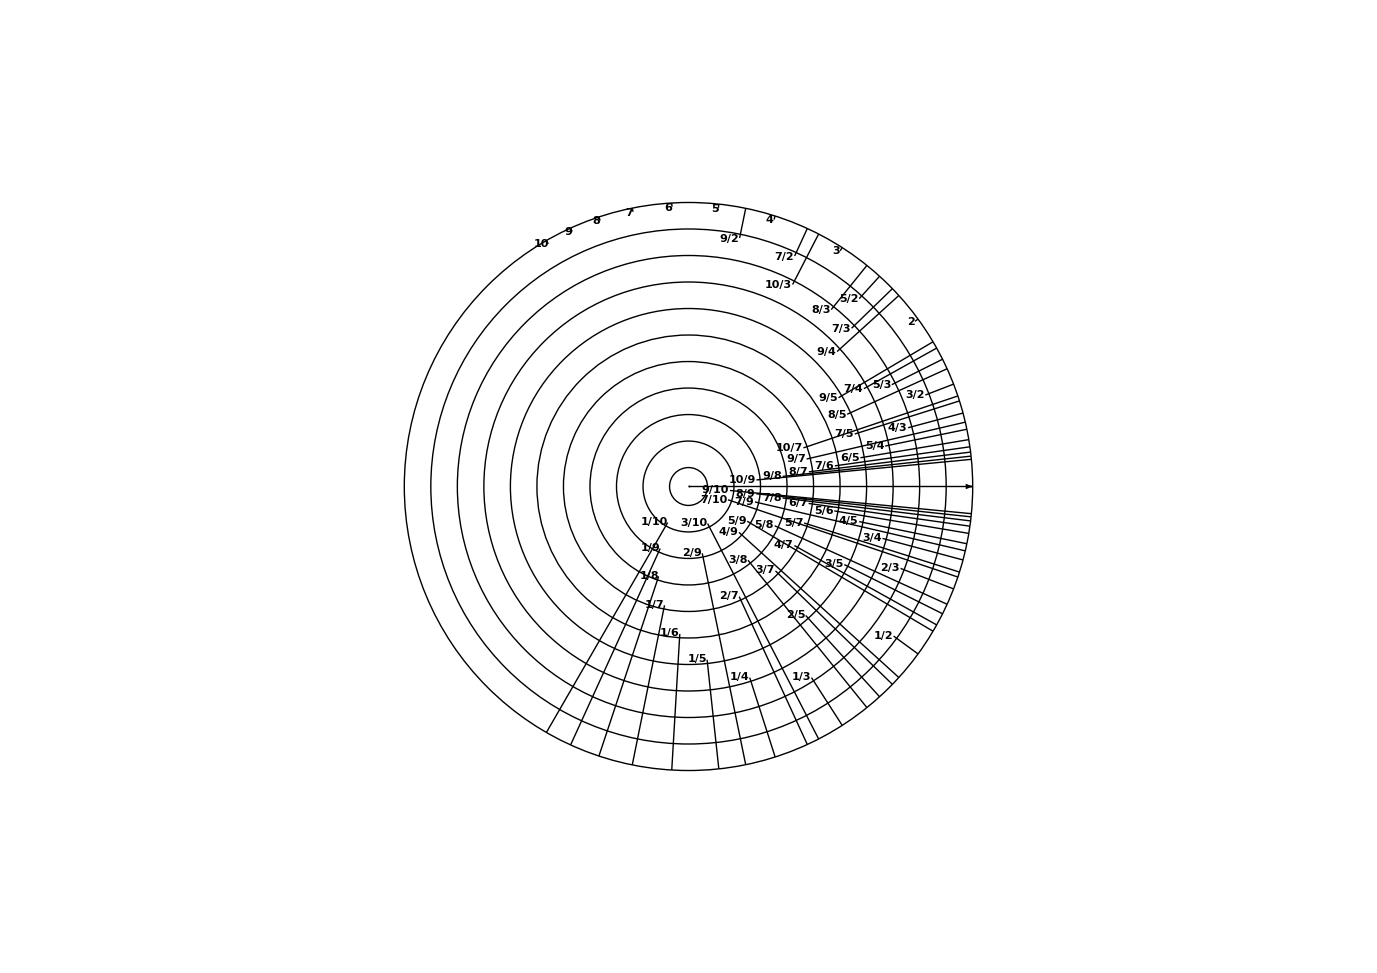

```mathematica
upper = Show[
Graphics[drawTick[r , r - 1 , -0.2,0.01 , None , shuffle->True]/@fractionFull],
Graphics[drawTick[r , r - 1 , -0.2,0.01 , None , invert->True , shuffle->True]/@fractionFullR],
Graphics[{{PointSize[Scaled[0.001]],Point[{0,0}]} , Circle[{0 , 0} , r] , {Thin , Table[Circle[{0 , 0} , r - i * 7] , {i ,1 , 10}]},{Thin , Arrowheads[Small],Arrow[{{0 , 0} , {r , 0}}]}}],
PlotRange->{{-0.5 * 297,0.5  297},{-0.5 * 210 , 0.5 * 210}}
]
```

```mathematica
Export[NotebookDirectory[]<>"upper.pdf",upper]
```

/home/kacper/Documents/upper.pdf

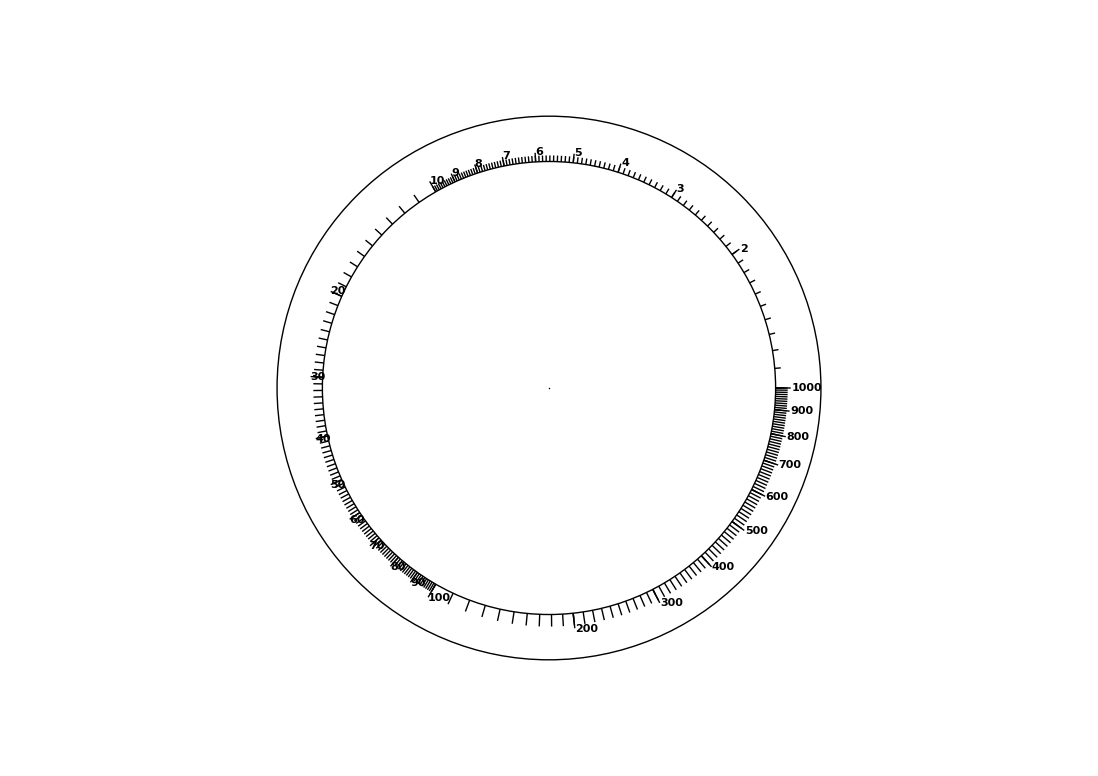

```mathematica
lower = Show[
Graphics[drawTick[r , r + 4 , 0.2,0.015 , True]/@regularFineScaleNamed],
Graphics[drawTick[r , r + 3 , 0.2,0.015 , True]/@regularExtraFineScaleNamed],
Graphics[drawTick[r , r + 5 , 0.2,0.015 , True]/@regularScale],
Graphics[drawTickSimple[r , r + 4]/@regularFineScale],
Graphics[drawTickSimple[r , r + 3]/@regularExtraFineScale] ,
Graphics[drawTickSimple[r , r + 2]/@regularExtraExtraFineScale] ,
Graphics[{PointSize[Scaled[0.001]],Point[{0,0}] , Circle[{0 , 0} , r],{Thin , Circle[{0 , 0} , r + space]}}],
PlotRange->{{-0.5 * 297,0.5  297},{-0.5 * 210 , 0.5 * 210}}
]
```

```mathematica
Export[NotebookDirectory[]<>"lower.pdf",lower]
```

/home/kacper/Documents/lower.pdf

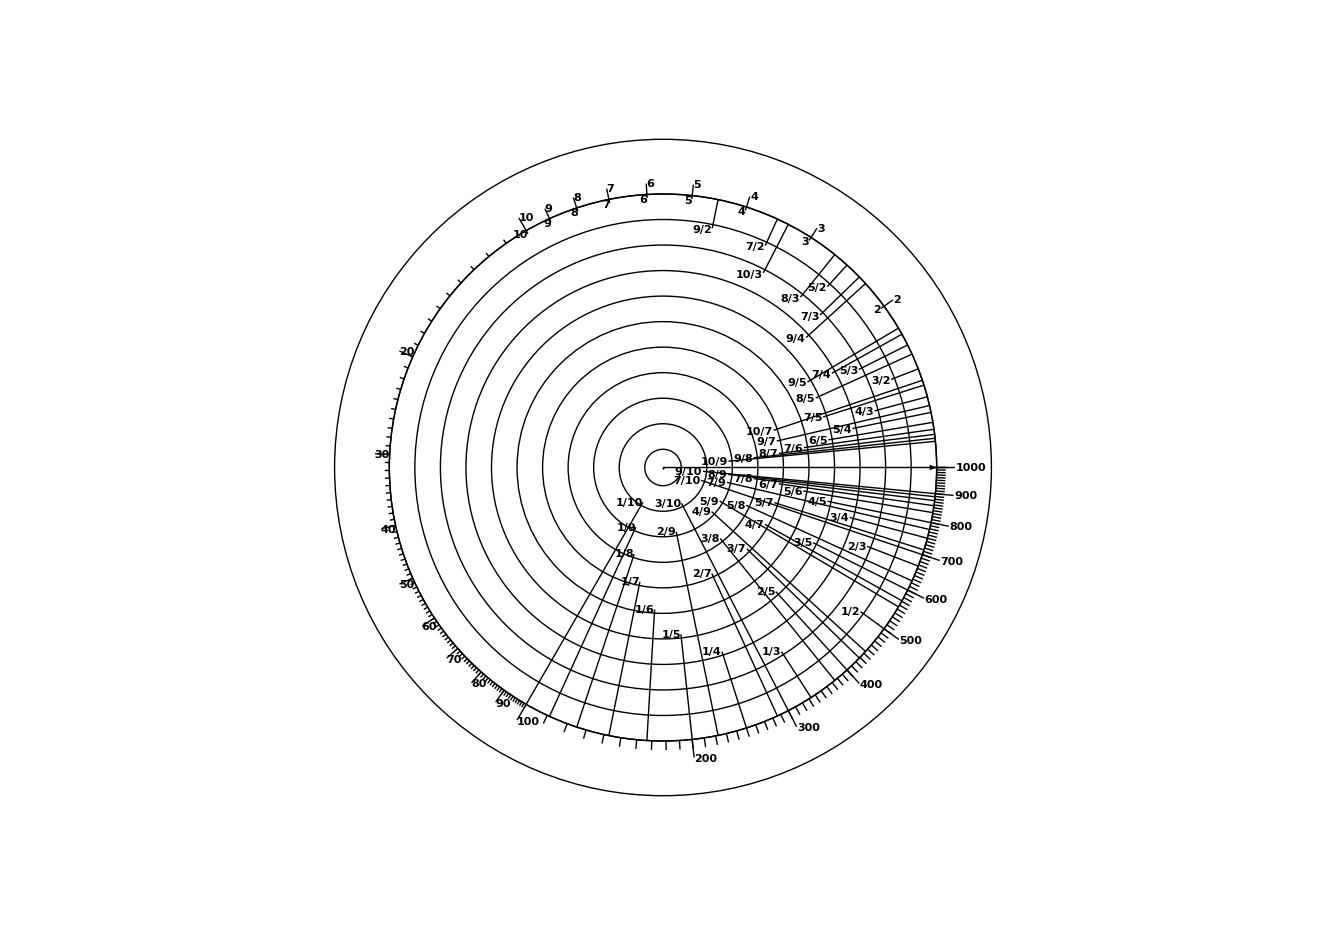

```mathematica
both = Show[
upper,
lower,
PlotRange->{{-0.5 * 297,0.5  297},{-0.5 * 210 , 0.5 * 210}}
]
```

```mathematica
Export[NotebookDirectory[]<>"both.pdf",both]
```

/home/kacper/Documents/both.pdf